```mathematica
Conway's Game of Life - Crappy Mathematica Edition
Miles Zimmerman
```

```mathematica
(* Calculate safe rows and columns, because mathematica has problems with 0 index *)
SafeIndex[indexSI_,opSI_,maxSI_] :=
Module[{index=indexSI,op=opSI,max=maxSI},
If[op==-1&&index==1,Return[-1]]; 
If[op==-1&&index >1,Return[index-1]];
If[op==+1&&index==max,Return[1]];
If[op==+1&&index <max,Return[index+1]];
]
```

```mathematica
(* Count neighbors of cell in matrix *)
CountNeighbors[matrixCN_, cellCN_]:=
Module[{matrix=matrixCN, cell=cellCN,totalNeighbors,matrixSize},
totalNeighbors = 0;
matrixSize = Dimensions[matrix];
(* -1,-1 *)
totalNeighbors=totalNeighbors+matrix[[SafeIndex[cell[[1]],-1,matrixSize[[1]]],SafeIndex[cell[[2]],-1,matrixSize[[2]]]]];
(* -1, 0 *)
totalNeighbors=totalNeighbors+matrix[[SafeIndex[cell[[1]],-1,matrixSize[[1]]],cell[[2]]]];
(* -1,+1 *)
totalNeighbors=totalNeighbors+matrix[[SafeIndex[cell[[1]],-1,matrixSize[[1]]],SafeIndex[cell[[2]],+1,matrixSize[[2]]]]];
(*  0,-1 *)
totalNeighbors=totalNeighbors+matrix[[cell[[1]],SafeIndex[cell[[2]],-1,matrixSize[[2]]]]];
(*  0,+1 *)
totalNeighbors=totalNeighbors+matrix[[cell[[1]],SafeIndex[cell[[2]],+1,matrixSize[[2]]]]];
(* +1,-1 *)
totalNeighbors=totalNeighbors+matrix[[SafeIndex[cell[[1]],+1,matrixSize[[1]]],SafeIndex[cell[[2]],-1,matrixSize[[2]]]]];
(* +1, 0 *)
totalNeighbors=totalNeighbors+matrix[[SafeIndex[cell[[1]],+1,matrixSize[[1]]],cell[[2]]]];
(* +1,+1 *)
totalNeighbors=totalNeighbors+matrix[[SafeIndex[cell[[1]],+1,matrixSize[[1]]],SafeIndex[cell[[2]],+1,matrixSize[[2]]]]];
Return[totalNeighbors]
]
```

```mathematica
(* Determine if cell born, lives, or dies *)
LiveAndLetDie[currentValueLLD_,numNeighborsLLD_] :=
Module[{currentValue=currentValueLLD,numNeighbors=numNeighborsLLD},
If[currentValue==0&&numNeighbors==3,Return[1]];
If[currentValue==0&&numNeighbors≠3,Return[0]];
If[currentValue==1&&(numNeighbors==2||numNeighbors==3),Return[1]];
If[currentValue==1&&numNeighbors<2,Return[0]];
If[currentValue==1&&numNeighbors>3,Return[0]];
]
```

```mathematica
(* Run the game of life *)
Life[startingMatrixL_,numRoundsL_]:=
Module[{startingMatrix=startingMatrixL,numRounds=numRoundsL,matrixSize,activeMatrix,referenceMatrix},
matrixSize=Dimensions[startingMatrix];
activeMatrix       =startingMatrix;
Do[
Do[
referenceMatrix=activeMatrix;
activeMatrix[[i,j]]=LiveAndLetDie[
referenceMatrix[[i,j]],
CountNeighbors[referenceMatrix,{i,j}]
],
{i,matrixSize[[1]]},
{j,matrixSize[[2]]}
],
{numRounds}
]
activeMatrix
]
```

```mathematica
(* 4x4 test matrix with 1 in each corner *)
testMatrix={{1,0,0,1},{0,0,0,0},{0,0,0,0},{1,0,0,1}};
```

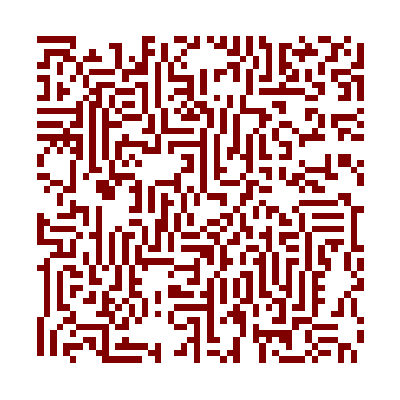

```mathematica
(* Game settings *)
sizeOfBoard        = 50;
numberOfRounds = 100;

(* Generate random board and run *)
randMatrix = Table[RandomInteger[],{sizeOfBoard},{sizeOfBoard}];
Life[randMatrix,numberOfRounds]//ArrayPlot
```